```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### When does λ_TF = λ_e? Critical electron density when EM radiation “shut offs”

```mathematica
Solve[λTF==1/me/.{Ef->(3 Pi^2 n)^(1/3)},n]
```

{{n→-me^3/(6 √(2 π) Z^(3/2) α^(3/2))},{n→me^3/(6 √(2 π) Z^(3/2) α^(3/2))}}

```mathematica
Convert[(me^3/(6 √(2 π) Z^(3/2) α^(3/2))/.{me->0.511,α->1/137,Z->6})(Mega ElectronVolt)^3*(200Mega ElectronVolt*Fermi)^-3,Centimeter^-3]
```

```mathematica
Convert[(1.2100003724836009*^32)/Centimeter^3*(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]
```

0.968 ElectronVolt^3 Mega^3

#### Plasma Frequency in relevant range of WD densities

```mathematica
Convert[((ni Z^2 e^2)/mi)^(1/2)*(200 Mega ElectronVolt*Fermi)^(3/2)/.{ni->10^29 Centimeter^-3,mi->12Giga ElectronVolt,e->0.3,Z->6},Kilo ElectronVolt]
```

0.464758 ElectronVolt Kilo

```mathematica
Convert[((n Z^2 e^2)/m)^(1/2)*(200 Mega ElectronVolt*Fermi)^(3/2)/.{n->10^32 Centimeter^-3,m->0.5 Mega ElectronVolt,e->0.3,Z->1},Mega ElectronVolt]
```

0.379473 ElectronVolt Mega

#### At what density does electron plasma freq = me?

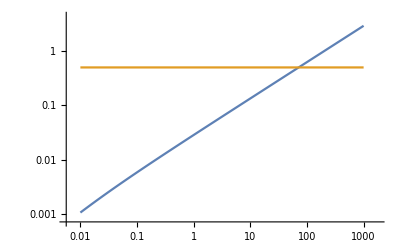

```mathematica
LogLogPlot[{(0.18 n)/(√(1+38.28312000250922 n^(2/3))),0.5},{n,0.01,1000}]
```

#### Classic EM cascades (Bethe-Heitler formulae):

```mathematica
BH=(k^2/ϵ^2+2 (1+(1-k/ϵ)^2))/(3 k n X0);
```

```mathematica
Integrate[BH*n*k,{k,0,ϵ}]
```

ϵ/X0

```mathematica
PP=(1+2 ((1-ϵ/k)^2+ϵ^2/k^2))/(3 k n X0);
```

```mathematica
Integrate[PP,{ϵ,0,k}]
```

7/(9 n X0)

#### LPM Energy

```mathematica
Convert[(m^2 X0 α)/(4Pi)/.X0->(4n Z^2 α^3/m^2)^-1*(200 Mega ElectronVolt*Fermi)^-3/.{m->0.511 Mega ElectronVolt,α-> 1/137,Z->6,n->10^31 Centimeter^-3},Mega ElectronVolt]
```

8.84021 ElectronVolt Mega

#### LPM Suppression

```mathematica
bremLPM=Integrate[√((Elpm k)/(ϵ (ϵ-k)))(k^2/ϵ^2+2 (1+(1-k/ϵ)^2))/(3 k n X0)*k*n,{k,0,ϵ}];
```

```mathematica
bremLPM//N
```

(1.50535 √(Elpm/ϵ) ϵ)/X0

```mathematica
ppLPM=Integrate[√((Elpm k)/(e(k-e)))(1+2 ((1-e/k)^2+e^2/k^2))/(3 k n X0),{e,0,k}];
```

```mathematica
ppLPM//N
```

(2.61799 √(Elpm/k))/(n X0)

#### Direct PP

```mathematica
dPPdata=Import["/Users/NewUser/Documents/Qballs/dpp.csv"];
```

```mathematica
dPP=Interpolation[dPPdata];
```

```mathematica
dPPplot=Plot[dPP[e],{e,14,26},PlotStyle->Gray];
```

InterpolatingFunction::dmval: Input value {14.0002} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Convert[300 Tera ElectronVolt,ElectronVolt]//N
```

3.×10^14 ElectronVolt

```mathematica
Convert[(e n Z^2 α^4)/m^2 10*(200 Mega ElectronVolt*Fermi)^2/.{n->10^23 Centimeter^-3,α->1/137,m->0.511 Mega ElectronVolt,Z->6},1/Meter]*Meter//N
```

0.0156545 e

```mathematica
dPPcalc=Plot[Log10[0.015654471965760308 10^e((3.*^14)/10^e)^(1/3)],{e,14,26},PlotStyle->{Thick}];
```

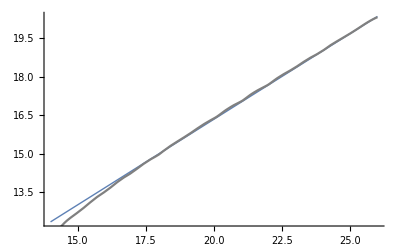

```mathematica
Show[dPPcalc,dPPplot]
```

#### eA interactions

```mathematica
eAdata=Import["/Users/NewUser/Documents/Qballs/eA.csv"];
```

```mathematica
eA=Interpolation[eAdata];
```

```mathematica
eAplot=Plot[eA[e],{e,14,26},PlotStyle->Gray];
```

InterpolatingFunction::dmval: Input value {14.0002} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Convert[10e n α σγ/.{n->10^23 Centimeter^-3,σγ->1 Milli Barn*(e/10^14)^0.08,α->1/137},1/Meter]//N
```

(0.0000553706 e^1.08)/Meter

```mathematica
(3.830711388684471*^-6 (10^e)^1.08)/Meter
```

```mathematica
eAcalc=Plot[Log10[0.00005537062591453895 (10^e)^1.08],{e,14,26},PlotStyle->{Thick}];
```

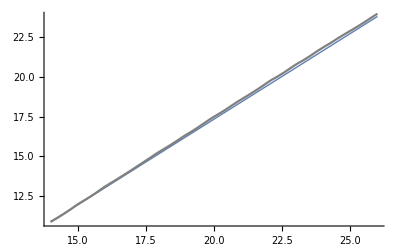

```mathematica
Show[eAcalc,eAplot]
```

#### Actual model - Klein

```mathematica
Integrate[((2α)/(Pi k)(((2e-k)^2+k^2)/(2 e^2)10-1)σγ*k*n),{k,10^-5 e,e}]//N
```

7.85152 e n α σγ

#### Stopping powers

```mathematica
brem=Piecewise[{{(√(Elpm/ϵ) ϵ)/X0,Elpm≤ϵ≤m^4/(16 n π Z α^4)},{ϵ/X0,ϵ≤Elpm}}];
bremalpha=If[m^4/(16 n π Z α^4)≤ϵ,(√(Elpm/ϵ) ϵ)/X0,0];
pp=Piecewise[{{(√(Elpm/ϵ) ϵ)/X0,Elpm≤ϵ≤m^4/(16 n π Z α^4)},{ϵ/X0,1≤ϵ≤Elpm},{0,ϵ≤1}}];
directpp=Piecewise[{{(ϵ Z^2 α^4)/m^2(n/Z)10*(Elpm/ϵ)^(1/3),ϵ≥Elpm},{(ϵ Z^2 α^4)/m^2(n/Z)10,ϵ<Elpm}}];
electronuclear=Piecewise[{{10 ϵ α σγ(n/Z),ϵ≥10},{0,ϵ<10}}];
photonuclear=Piecewise[{{ϵ σγ(n/Z),ϵ≥10},{0,ϵ<10}}];
```

#### Plots of stopping powers

```mathematica
electronbrem=LogLogPlot[ReplaceAll[ReplaceAll[ReplaceAll[brem,{Elpm->(m^2 X0 α)/(4Pi)}],X0->(4 n/Z Z^2 α^3/m^2)^-1],{Z->6,α->1/137,m->0.511,n->0.8}](5.*^5),{ϵ,1,10^10},PlotStyle->{Green,Thick}];
electronbremalpha=LogLogPlot[ReplaceAll[ReplaceAll[ReplaceAll[bremalpha,{Elpm->(m^2 X0 α)/(4Pi)}],X0->(4 n/Z Z^2 α^3/m^2)^-1],{Z->6,α->1/137,m->0.511,n->0.8}](5.*^5),{ϵ,1,10^10},PlotStyle->{Green,Dashed}];
electrondpp=LogLogPlot[ReplaceAll[ReplaceAll[ReplaceAll[directpp,{Elpm->(m^2 X0 α)/(4Pi)}],X0->(4(n/Z)Z^2 α^3/m^2)^-1],{Z->6,α->1/137,m->0.511,n->0.8}](5.*^5),{ϵ,1,10^10},PlotStyle->{Red,Thick}];
electronhad=LogLogPlot[ReplaceAll[electronuclear,{σγ->10^-3,n->0.8,α->1/137,Z->6}](0.0025)(5.*^5),{ϵ,1,10^10},PlotStyle->{Purple,Thick}];
photonhad=LogLogPlot[ReplaceAll[photonuclear,{σγ->10^-3,n->0.8,α->1/137,Z->6}](0.0025)(5.*^5),{ϵ,1,10^10},PlotStyle->{Purple,Thick}];
photonpp=LogLogPlot[ReplaceAll[ReplaceAll[ReplaceAll[pp,{Elpm->(m^2 X0 α)/(4Pi)}],X0->(4 n/Z Z^2 α^3/m^2)^-1],{Z->6,α->1/137,m->0.511,n->0.8}](5.*^5),{ϵ,1,10^10},PlotStyle->{Green,Thick}];
```

#### When is brem/pp suppressed O(α)?

```mathematica
Solve[ReplaceAll[ReplaceAll[ √(Elpm/ϵ) ==α,{Elpm->(m^2 X0 α)/(4Pi)}],X0->(4(n/Z)Z^2 α^3/m^2)^-1],ϵ]//FullSimplify
```

```mathematica
{{ϵ->m^4/(16 n π Z α^4)Mega ElectronVolt}}/.{m->0.511,n->0.8,Z->6,α->1/137}//FullSimplify
```

{{ϵ→99553.1 ElectronVolt Mega}}